## Formulae an

```mathematica
ExplainContractionCounts[g_,e_]:=Block[{
gBis=SortGraph[g], 
taken={e[[1]],e[[2]]},
comp=SortGraph[VertexDelete[VertexDelete[GraphComplement[g],e[[1]]],e[[2]]]],
nonEdges=0,
remainingNonEdges=0,
result},
result=Table[
If[!EdgeQ[gBis,e[[1]]<->v]&&!EdgeQ[gBis,e[[2]]<->v],
nonEdges++
]
,{v,Select[VertexList[gBis],!MemberQ[taken,#]&]}
];
remainingNonEdges=Length[EdgeList[comp]];
{nonEdges,remainingNonEdges}
]
```

```mathematica
MpgChain[g_]:=Block[{contract, result},
If[VertexCount[g]==3,Return[{ChromaticPolynomial[g,4]/24}]];
Table[
contract=EdgeContract[g,e];
If[MaximalPlanarQ[contract],
result=Prepend[MpgChain[contract],{e,ChromaticPolynomial[g,4]/24}];
Goto[stop]
]
,{e,EdgeList[g]}
];
Label[stop];
result
]
```

```mathematica
MpgChain3[g_]:=Block[{contract, result},
If[VertexCount[g]==3,Return[{ChromaticPolynomial[g,4]/24}]];
Table[
contract=EdgeContract[g,e];
If[MaximalPlanarQ[contract],
result=Prepend[MpgChain3[contract],ChromaticPolynomial[g,4]/24];
Goto[stop]
]
,{e,EdgeList[g]}
];
Label[stop];
result
]
```

```mathematica
Monitor[Select[Table[k->With[{l=Differences[Reverse[MpgChain3[ReadGrof[k]]]]},{Min[l],Max[l]}],{k,10}],#[[2]]≠{0,0}&],k]
```

{4→{0,3},6→{0,3},7→{0,3}}

```mathematica
cm=72/2.54;
```

```mathematica
Clear[MpgChain2]
```

```mathematica
SymbolToColoring[First[FindFullFormula4[Graph[plantri [[1]] ]]]]
```

{1→RGBColor[1, 0, 0],9→RGBColor[1, 0, 0],11→RGBColor[1, 0, 0],2→RGBColor[0, 0, 1],5→RGBColor[0, 0, 1],12→RGBColor[0, 0, 1],3→RGBColor[1, 1, 0],7→RGBColor[1, 1, 0],10→RGBColor[1, 1, 0],4→RGBColor[0, 1, 0],6→RGBColor[0, 1, 0],8→RGBColor[0, 1, 0]}

```mathematica
MpgChain2[g_]:=Block[{ layout, fullForm,form,edge,  graphs, neighbors},
If[VertexCount[g]==2,Return[{}]];
edge=First[CollectMPGEdges[g]];
fullForm=FindFullFormula4[g];
graphs=Table[NeighborhoodGraph[g,v],{v,{edge[[1]],edge[[2]]}}];
neighbors=GraphUnion[graphs[[1]],graphs[[2]]];
Graph[
g,
GraphHighlightStyle->"Thick",
GraphHighlight->EdgeList[neighbors],
VertexLabels->"Name",
VertexLabelStyle->Directive[Darker[Green],Italic,10],
ImageSize->{10 cm, 10 cm}, 
AspectRatio->1,
VertexSize->Map[#->If[MemberQ[{edge[[1]],edge[[2]]},#],1,0.6]&,VertexList[g]],
GraphLayout->"PlanarEmbedding"
]->
Table[
form=SymbolToColoring[symbol];
With[{sub=Graph[
EdgeList[neighbors],
VertexLabels->"Name",
VertexLabelStyle->Directive[Darker[Green],Italic,10],
ImageSize->{10 cm, 10 cm}, 
AspectRatio->1,
VertexStyle->Select[form,MemberQ[VertexList[neighbors],#[[1]]]&],
VertexSize->Map[#->If[MemberQ[{edge[[1]],edge[[2]]},#],Large,Medium]&,VertexList[neighbors]],
GraphLayout->"PlanarEmbedding"
]},
Labeled[
Graph[
sub,
GraphHighlight->Select[CollectMPGEdges[g],EdgeQ[sub,#]&]
],
{SymbolToLabel[symbol],Map[SymbolToLabel,FindFullFormula4[sub]]
}
]
]
,
{symbol, fullForm}
]
]
```

## experiments come

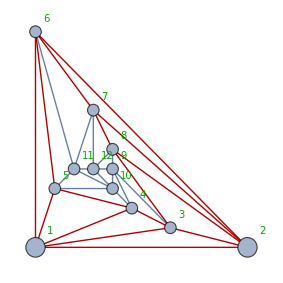
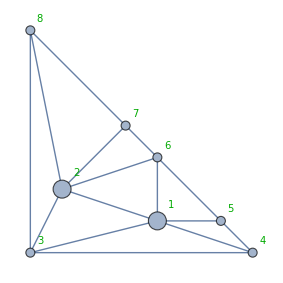
-Graphics-→{-Graphics-{19b♁25c♁37a♁468,{1♁2♁357♁468,1♁25♁37♁468,1♁24♁357♁68,18♁2♁357♁46,18♁25♁37♁46,18♁25♁36♁47,18♁24♁36♁57,18♁24♁357♁6,17♁2♁35♁468,17♁25♁3♁468,17♁25♁36♁48,17♁24♁36♁58,17♁24♁35♁68}},-Graphics-{19b♁24c♁357♁68a,{1♁2♁357♁468,1♁25♁37♁468,1♁24♁357♁68,18♁2♁357♁46,18♁25♁37♁46,18♁25♁36♁47,18♁24♁36♁57,18♁24♁357♁6,17♁2♁35♁468,17♁25♁3♁468,17♁25♁36♁48,17♁24♁36♁58,17♁24♁35♁68}},-Graphics-{18a♁29b♁357♁46c,{1♁2♁357♁468,1♁25♁37♁468,1♁24♁357♁68,18♁2♁357♁46,18♁25♁37♁46,18♁25♁36♁47,18♁24♁36♁57,18♁24♁357♁6,17♁2♁35♁468,17♁25♁3♁468,17♁25♁36♁48,17♁24♁36♁58,17♁24♁35♁68}},-Graphics-{18b♁259♁37a♁46c,{1♁2♁357♁468,1♁25♁37♁468,1♁24♁357♁68,18♁2♁357♁46,18♁25♁37♁46,18♁25♁36♁47,18♁24♁36♁57,18♁24♁357♁6,17♁2♁35♁468,17♁25♁3♁468,17♁25♁36♁48,17♁24♁36♁58,17♁24♁35♁68}},-Graphics-{18b♁24c♁36a♁579,{1♁2♁357♁468,1♁25♁37♁468,1♁24♁357♁68,18♁2♁357♁46,18♁25♁37♁46,18♁25♁36♁47,18♁24♁36♁57,18♁24♁357♁6,17♁2♁35♁468,17♁25♁3♁468,17♁25♁36♁48,17♁24♁36♁58,17♁24♁35♁68}},-Graphics-{18a♁24b♁36c♁579,{1♁2♁357♁468,1♁25♁37♁468,1♁24♁357♁68,18♁2♁357♁46,18♁25♁37♁46,18♁25♁36♁47,18♁24♁36♁57,18♁24♁357♁6,17♁2♁35♁468,17♁25♁3♁468,17♁25♁36♁48,17♁24♁36♁58,17♁24♁35♁68}},-Graphics-{17a♁29b♁35c♁468,{1♁2♁357♁468,1♁25♁37♁468,1♁24♁357♁68,18♁2♁357♁46,18♁25♁37♁46,18♁25♁36♁47,18♁24♁36♁57,18♁24♁357♁6,17♁2♁35♁468,17♁25♁3♁468,17♁25♁36♁48,17♁24♁36♁58,17♁24♁35♁68}},-Graphics-{17a♁259♁36c♁48b,{1♁2♁357♁468,1♁25♁37♁468,1♁24♁357♁68,18♁2♁357♁46,18♁25♁37♁46,18♁25♁36♁47,18♁24♁36♁57,18♁24♁357♁6,17♁2♁35♁468,17♁25♁3♁468,17♁25♁36♁48,17♁24♁36♁58,17♁24♁35♁68}},-Graphics-{179♁25c♁36a♁48b,{1♁2♁357♁468,1♁25♁37♁468,1♁24♁357♁68,18♁2♁357♁46,18♁25♁37♁46,18♁25♁36♁47,18♁24♁36♁57,18♁24♁357♁6,17♁2♁35♁468,17♁25♁3♁468,17♁25♁36♁48,17♁24♁36♁58,17♁24♁35♁68}},-Graphics-{179♁24b♁35c♁68a,{1♁2♁357♁468,1♁25♁37♁468,1♁24♁357♁68,18♁2♁357♁46,18♁25♁37♁46,18♁25♁36♁47,18♁24♁36♁57,18♁24♁357♁6,17♁2♁35♁468,17♁25♁3♁468,17♁25♁36♁48,17♁24♁36♁58,17♁24♁35♁68}}}

```mathematica
MpgChain2[Graph[plantri [[1]] ] ]
```

```mathematica
EdgeList[Graph[plantri [[1]] ]]
```

{1<->2,1<->3,1<->4,1<->5,1<->6,2<->6,2<->7,2<->8,2<->3,3<->8,3<->9,3<->4,4<->9,4<->10,4<->5,5<->10,5<->11,5<->6,6<->11,6<->7,7<->11,7<->12,7<->8,8<->12,8<->9,9<->12,9<->10,10<->12,10<->11,11<->12}

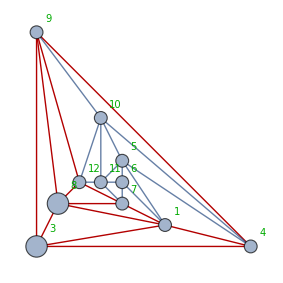
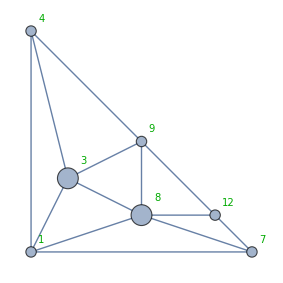
-Graphics-→{-Graphics-19b♁37a♁468♁5c,-Graphics-19b♁37a♁46c♁58,-Graphics-1c♁36a♁48b♁579,-Graphics-1a♁36c♁48b♁579,-Graphics-19b♁357♁4c♁68a,-Graphics-19b♁35c♁47♁68a,-Graphics-19b♁357♁46c♁8a,-Graphics-19b♁35c♁468♁7a}

```mathematica
MpgChain2[EdgeContract[Graph[plantri [[1]] ],1<->2] ]
```

```mathematica
MpgChain2[Graph[plantri [[5]] ] ]
```

$Aborted

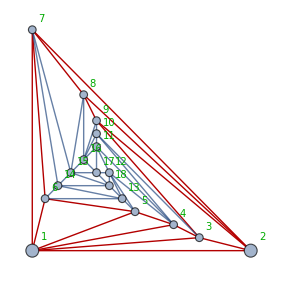
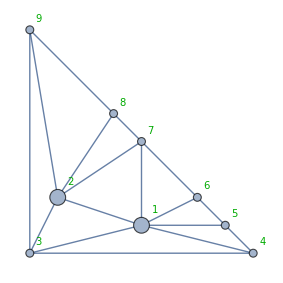
-Graphics-→{-Graphics-1gi♁26acf♁358be♁479dh,-Graphics-1eg♁26acf♁358bi♁479dh,-Graphics-1ceg♁26af♁358bi♁479dh,-Graphics-1ceg♁25af♁368bi♁479dh,-Graphics-1acf♁26gi♁358be♁479dh,-Graphics-1acf♁25eg♁368bi♁479dh,-Graphics-1acf♁246gi♁358eh♁79bd,-Graphics-1acf♁246gi♁358be♁79dh,-Graphics-19bdf♁2ace♁357gi♁468h,-Graphics-19be♁26acf♁357gi♁48dh,-Graphics-19bd♁26acf♁357gi♁48eh,-Graphics-19bdf♁26ac♁357gi♁48eh,-Graphics-19bi♁26acf♁358eh♁47dg,-Graphics-19bd♁26acf♁358eh♁47gi,-Graphics-19bdf♁26ac♁358eh♁47gi,-Graphics-19dh♁26acf♁358be♁47gi,-Graphics-19eh♁26acf♁358bi♁47dg,-Graphics-19bdf♁25aeh♁37cg♁468i,-Graphics-19bdf♁25aeh♁368c♁47gi,-Graphics-19cf♁25aeh♁368bi♁47dg,-Graphics-19bdf♁246gi♁38ce♁57ah,-Graphics-19bdf♁246i♁37cg♁58aeh,-Graphics-19bdf♁246gi♁37c♁58aeh,-Graphics-19cf♁246gi♁37bd♁58aeh,-Graphics-19bdf♁246h♁357gi♁8ace,-Graphics-19bdf♁246gi♁357h♁8ace,-Graphics-19bdf♁246gi♁358eh♁7ac,-Graphics-19cf♁246gi♁358be♁7adh,-Graphics-19bdf♁24eh♁357gi♁68ac,-Graphics-18adh♁2ceg♁357bi♁469f,-Graphics-18ace♁2bdf♁357gi♁469h,-Graphics-18ace♁26bf♁357gi♁49dh,-Graphics-18be♁26acf♁357gi♁49dh,-Graphics-18bd♁26acf♁357gi♁49eh,-Graphics-18aeh♁26cg♁357bi♁49df,-Graphics-18bi♁26acf♁35eg♁479dh,-Graphics-18ace♁26gi♁35bf♁479dh,-Graphics-18ace♁26bf♁35gi♁479dh,-Graphics-18be♁26acf♁35gi♁479dh,-Graphics-18ace♁25gi♁36bf♁479dh,-Graphics-18ace♁25bf♁36gi♁479dh,-Graphics-18adh♁246f♁3ceg♁579bi,-Graphics-18ace♁246gi♁3bdf♁579h,-Graphics-18ace♁246gi♁37dh♁59bf,-Graphics-18aeh♁24df♁36cg♁579bi,-Graphics-18aeh♁24dg♁36cf♁579bi,-Graphics-18adh♁24eg♁36cf♁579bi,-Graphics-18ace♁246h♁357gi♁9bdf,-Graphics-18ace♁246gi♁357h♁9bdf,-Graphics-18ace♁246gi♁35bf♁79dh,-Graphics-18ace♁24dh♁357gi♁69bf,-Graphics-18aeh♁24dg♁357bi♁69cf,-Graphics-18adh♁24eg♁357bi♁69cf}

```mathematica
MpgChain2[Graph[plantri [[20]] ] ]
```